```mathematica
g[y_]:={{1,0},{0,1+(z'[y])^2}}
```

```mathematica
detg[y_]:=Det[g[y]]
```

```mathematica
sqrtdetg[y_]:=Sqrt[detg[y]]
```

```mathematica
H[y_]:=1/2/( detg[y])^(3/2)z''[y]
```

```mathematica
σ[y_]:=σ0
```

```mathematica
(*solve for n^i omega_i == ψTOP at \partial \Omega_TOP*)
```

```mathematica
solTOP=Flatten[Solve[1/sqrtdetg[y] z'[y]==ψTOP,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψTOP/(√(1-ψTOP^2))

```mathematica
solBOTTOM=Flatten[Solve[-1/sqrtdetg[y] z'[y]==ψBOTTOM,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψBOTTOM/(√(1-ψBOTTOM^2))

```mathematica
L=10;
h=1;
κ=1;
σ0=1;
CC=1/100;
DD=1/100;
ϕTOP=CC;
ϕBOTTOM=0;
ψTOP=DD;
ψBOTTOM=0;
```

```mathematica
eq={κ(-(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]-2( H[y])^3)+ σ [y]H[y]==0}//FullSimplify
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0}

```mathematica
bcs={z[0]==ϕBOTTOM,z[h]==ϕTOP,z'[0]==(z'[y]/.solBOTTOM),z'[h]==(z'[y]/.solTOP)}
```

{z[0]==0,z[1]==1/100,z'[0]==0,z'[1]==1/(3 √1111)}

```mathematica
sys=Flatten[{eq,bcs}]
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0,z[0]==0,z[1]==1/100,z'[0]==0,z'[1]==1/(3 √1111)}

```mathematica
sol=NDSolve[sys,z,{y,0,h},WorkingPrecision->10]
```

{{z→InterpolatingFunction[…]}}

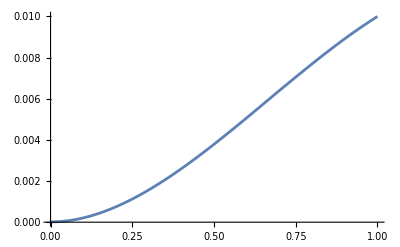

```mathematica
plotzexact=Plot[Evaluate[z[y]/.sol],{y,0,h},PlotRange->All]
```

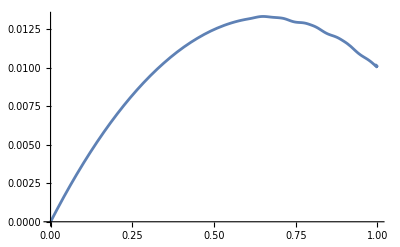

```mathematica
plotωexact=Plot[Evaluate[z'[y]/.sol],{y,0,h},PlotRange->All]
```

```mathematica
tabz=Table[{y,Evaluate[z[y]/.sol][[1]]},{y,0,h,h/10}]
tabω=Table[{y,Evaluate[z'[y]/.sol][[1]]},{y,0,h,h/10}]
```

{{0,0.00001395628},{1/10,0.00020807504},{1/5,0.00074672477},{3/10,0.0015642551},{2/5,0.002597738},{1/2,0.0037865383},{3/5,0.00507157117},{7/10,0.00639716568},{4/5,0.00769577877},{9/10,0.0089163182},{1,0.01}}

{{0,-8.3423×10^-6},{1/10,0.003775998},{1/5,0.006887756},{3/10,0.009357996},{2/5,0.01121182},{1/2,0.0124673},{3/5,0.01313697},{7/10,0.01322784},{4/5,0.01273939},{9/10,0.01166685},{1,0.0100005}}

```mathematica
NN=3;
```

```mathematica
fz[y_]:=Sum[c[i]y^i,{i,0,NN}]
fω[y_]:=Sum[d[i]y^i,{i,0,NN}]
```

```mathematica
fitz=FindFit[tabz,fz[y],Table[c[i],{i,0,NN}],y]
fitω=FindFit[tabω,fω[y],Table[d[i],{i,0,NN}],y]
```

{c[0]→0.00001102968,c[1]→0.0001220659,c[2]→0.01983687,c[3]→-0.009972405}

{d[0]→9.7371×10^-6,d[1]→0.040693,d[2]→-0.032282,d[3]→0.0015978}

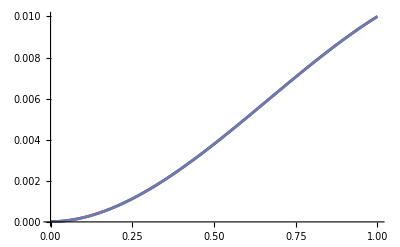

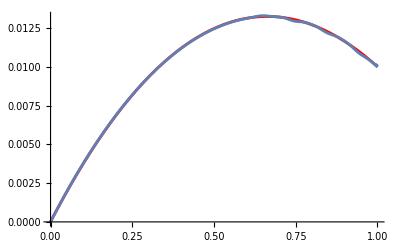

```mathematica
Show[Plot[fz[y]/.fitz,{y, 0,h},PlotStyle->Red],plotzexact]
Show[Plot[fω[y]/.fitω,{y, 0,h},PlotStyle->Red],plotωexact]
```

```mathematica
fz[y]/.fitz
fω[y]/.fitω
```

0.00001102968+0.0001220659 y+0.01983687 y^2-0.009972405 y^3

9.7371×10^-6+0.040693 y-0.032282 y^2+0.0015978 y^3

```mathematica
t=Import["~/Documents/finite_elements/solution/z.csv"];
t=Table[{t[[i,3]],If[Abs[t[[i,2]]-L/2]<0.1,t[[i,1]],0]},{i,2,Length[t]}]
```

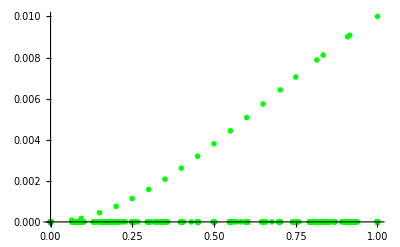

```mathematica
plotnum=ListPlot[t,PlotStyle->{Green,PointSize->0.01}]
```

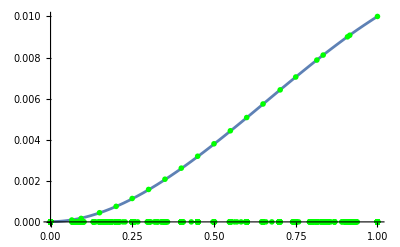

```mathematica
Show[plotzexact,plotnum]
```